# Integrals containing spherical bessel functions

## Intro

We are intereted in the integlals of form:

   I_(l_1... l_n)(r_1... r_n)= ∫_0^∞ ⅆk f(k)j_l_1(k r_1)...j_l_n(k r_n).

In order for this integral to exist we have a conditions on f(k).

```mathematica
MyExp[X_]:=With[{cmuopt=SystemOptions["CatchMachineUnderflow"]},Internal`WithLocalSettings[SetSystemOptions["CatchMachineUnderflow"->False],
Exp[X],SetSystemOptions[cmuopt]]]
```

```mathematica
Clear[SinCosBess]
SinCosBess[n_,x_]:=Block[{tmp},
tmp=(SphericalBesselJ[n,x]//FunctionExpand);
Return[{tmp/.{Cos[__]->0,Sin[__]->1},
tmp/.{Cos[__]->1,Sin[__]->0}}]
]
```

```mathematica
Exp[-1/100.]
```

0.99005

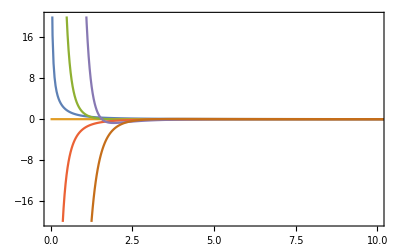

```mathematica
Plot[(1-Exp[-1/x]){SinCosBess[0,x],SinCosBess[2,x],SinCosBess[4,x]}//Evaluate,{x,0,100},PlotRange->{{0,10},{-20,20}},Frame->True]
```

```mathematica
Clear[SinCosExpand]
SinCosExpand[x_]:=Block[{tmp},
tmp=(((x//FunctionExpand)//Expand)//TrigReduce)//Collect[#,{Cos[_],Sin[_]}]&;
Return[tmp]]
```

```mathematica
SinCosExpand[SphericalBesselJ[1,k x[1]]SphericalBesselJ[2,k x[2]]SphericalBesselJ[1,k x[3]]]
```

Cos[k x[1]+k x[2]+k x[3]] (3/(4 k^6 x[1] x[2]^3 x[3]^2)+3/(4 k^6 x[1]^2 x[2]^2 x[3]^2)-1/(4 k^4 x[1] x[2] x[3]^2)+3/(4 k^6 x[1]^2 x[2]^3 x[3])-3/(4 k^4 x[1] x[2]^2 x[3])-1/(4 k^4 x[1]^2 x[2] x[3]))+Cos[k x[1]+k x[2]-k x[3]] (-3/(4 k^6 x[1] x[2]^3 x[3]^2)-3/(4 k^6 x[1]^2 x[2]^2 x[3]^2)+1/(4 k^4 x[1] x[2] x[3]^2)+3/(4 k^6 x[1]^2 x[2]^3 x[3])-3/(4 k^4 x[1] x[2]^2 x[3])-1/(4 k^4 x[1]^2 x[2] x[3]))+Cos[k x[1]-k x[2]-k x[3]] (3/(4 k^6 x[1] x[2]^3 x[3]^2)-3/(4 k^6 x[1]^2 x[2]^2 x[3]^2)-1/(4 k^4 x[1] x[2] x[3]^2)-3/(4 k^6 x[1]^2 x[2]^3 x[3])-3/(4 k^4 x[1] x[2]^2 x[3])+1/(4 k^4 x[1]^2 x[2] x[3]))+Cos[k x[1]-k x[2]+k x[3]] (-3/(4 k^6 x[1] x[2]^3 x[3]^2)+3/(4 k^6 x[1]^2 x[2]^2 x[3]^2)+1/(4 k^4 x[1] x[2] x[3]^2)-3/(4 k^6 x[1]^2 x[2]^3 x[3])-3/(4 k^4 x[1] x[2]^2 x[3])+1/(4 k^4 x[1]^2 x[2] x[3]))+Sin[k x[1]+k x[2]-k x[3]] (3/(4 k^7 x[1]^2 x[2]^3 x[3]^2)-3/(4 k^5 x[1] x[2]^2 x[3]^2)-1/(4 k^5 x[1]^2 x[2] x[3]^2)+3/(4 k^5 x[1] x[2]^3 x[3])+3/(4 k^5 x[1]^2 x[2]^2 x[3])-1/(4 k^3 x[1] x[2] x[3]))+Sin[k x[1]+k x[2]+k x[3]] (-3/(4 k^7 x[1]^2 x[2]^3 x[3]^2)+3/(4 k^5 x[1] x[2]^2 x[3]^2)+1/(4 k^5 x[1]^2 x[2] x[3]^2)+3/(4 k^5 x[1] x[2]^3 x[3])+3/(4 k^5 x[1]^2 x[2]^2 x[3])-1/(4 k^3 x[1] x[2] x[3]))+Sin[k x[1]-k x[2]+k x[3]] (3/(4 k^7 x[1]^2 x[2]^3 x[3]^2)+3/(4 k^5 x[1] x[2]^2 x[3]^2)-1/(4 k^5 x[1]^2 x[2] x[3]^2)-3/(4 k^5 x[1] x[2]^3 x[3])+3/(4 k^5 x[1]^2 x[2]^2 x[3])+1/(4 k^3 x[1] x[2] x[3]))+Sin[k x[1]-k x[2]-k x[3]] (-3/(4 k^7 x[1]^2 x[2]^3 x[3]^2)-3/(4 k^5 x[1] x[2]^2 x[3]^2)+1/(4 k^5 x[1]^2 x[2] x[3]^2)-3/(4 k^5 x[1] x[2]^3 x[3])+3/(4 k^5 x[1]^2 x[2]^2 x[3])+1/(4 k^3 x[1] x[2] x[3]))

```mathematica
(*Map[x[1]+(Array[x,5])⟦2;;All⟧.#&,Tuples[{-1,1},4]]*)
```

By expanding the spherical bessel function we get

   I_(l_1... l_n)(r_1... r_n)=
=∑_(over q tuples) ( ∫_0^∞ ⅆk F_(l_1... l_n)^s(k|r_1... r_n)sin[k (r_1+q_2 r_2...+q_n r_n)]+ ∫_0^∞ ⅆk F_(l_1... l_n)^c(k|r_1... r_n)cos[k (r_1+q_2 r_2...+q_n r_n)])
=∑_(over q tuples) ( ∫_0^∞ ⅆk F_(l_1... l_n)^s(k|r_1... r_n)sin[k R_p]+ ∫_0^∞ ⅆk F_(l_1... l_n)^c(k|r_1... r_n)cos[k R_p])

The integlal above takes a form 
   I_(l_1... l_n)(r_1... r_n)=
=∑_(over q tuples) ∑_n a_n(r_1... r_n)∫_0^∞ ⅆk (f(k))/k^n sin[k R_p]+ b_n(r_1... r_n)∫_0^∞ ⅆk (f(k))/k^n cos[k R_p]

## IR regularization

The integlal above take a form 
   ∫_0^∞ ⅆk (f(k))/k^n sin[k R_p] = lim_(ϵ→ 0) ∫_0^∞ ⅆk W_ϵ(k) (f(k))/k^n sin[k R_p]

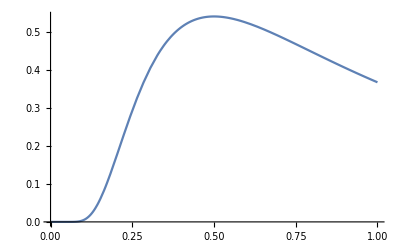

```mathematica
Plot[Exp[-ϵ/k]/k^n/.{ϵ->1.0,n->2},{k,0,1},PlotRange->All]
```

```mathematica
tmp=SinCosExpand[SphericalBesselJ[0,k x[1]]SphericalBesselJ[0,k x[2]]]
```

Cos[k x[1]-k x[2]]/(2 k^2 x[1] x[2])-Cos[k x[1]+k x[2]]/(2 k^2 x[1] x[2])

```mathematica
Series[tmp,{k,0,3}]
```

1+(-1/6 x[1]^2-x[2]^2/6) k^2+O[k]^4

## Examples

```mathematica
Clear[IntN]
IntN[x_,y_]:=NIntegrate[k^3 Exp[-k^2]SphericalBesselJ[3,k x]SphericalBesselJ[1,k y],{k,0,Infinity},PrecisionGoal->10];
```

```mathematica
Clear[IntNtab]
IntNtab=Table[{x,y,IntN[x,y]//Quiet},{x,0,5,0.25},{y,0,5,0.25}];
```

```mathematica
(*Clear[IntA1,IntA2,IntA3,IntA4,IntA5]
IntA1=Integrate[Evaluate[(k^3 Exp[-k^2]SphericalBesselJ[3,k x]SphericalBesselJ[1,k y]//FunctionExpand)//TrigToExp//Expand],{k,0,Infinity},Assumptions->x>=0&&y>=0];
IntA2=Series[IntA1,{x,0,4},Assumptions->x>0&&y>0]//Normal;
IntA3=Series[IntA1,{y,0,4},Assumptions->x>0&&y>0]//Normal;
IntA4=Series[IntA1,{x,0,4},{y,0,4},Assumptions->x>0&&y>0]//Normal;
IntA5[xx_,yy_]:=Block[{cut=1.0},Piecewise[{{IntA1/.{x->xx,y->yy},xx>=cut&&yy>=cut},{IntA2/.{x->xx,y->yy},xx<cut&&yy>=cut},{IntA3/.{x->xx,y->yy},xx>=cut&&yy<cut},{IntA4/.{x->xx,y->yy},xx<cut&&yy<cut}}]//N//Re];*)
```

```mathematica
(*Clear[IntAtab]
IntAtab=Table[{x,y,IntA5[x,y]},{x,0,5,0.1},{y,0,5,0.1}];*)
```

```mathematica
Show[ListPlot3D[IntNtab//Flatten[#,1]&,PlotStyle->Directive[PointSize[0.015],Blue,Opacity[0.25]],PlotRange->{-0.01,0.05}](*,
ListPlot3D[IntAtab//Flatten[#,1]&,PlotStyle->Opacity[0.5],PlotRange->{-0.15,0.15}]*)]
```

-Graphics3D-

```mathematica
SinCosExpand[SphericalBesselJ[3,k x]SphericalBesselJ[1,k y]]
```

(15/(2 k^6 x^4 y^2)-3/(k^4 x^2 y^2)+15/(2 k^4 x^3 y)-1/(2 k^2 x y)) Cos[k x-k y]+(-15/(2 k^6 x^4 y^2)+3/(k^4 x^2 y^2)+15/(2 k^4 x^3 y)-1/(2 k^2 x y)) Cos[k x+k y]+(15/(2 k^5 x^3 y^2)-1/(2 k^3 x y^2)-15/(2 k^5 x^4 y)+3/(k^3 x^2 y)) Sin[k x-k y]+(-15/(2 k^5 x^3 y^2)+1/(2 k^3 x y^2)-15/(2 k^5 x^4 y)+3/(k^3 x^2 y)) Sin[k x+k y]

```mathematica
FourierCosTransform[k^3 Exp[-k^2] 15/(2 k^6)(*Exp[1/k]*),k,ω,FourierParameters->{1,1}]
```

FourierCosTransform[(15 ⅇ^(-k^2))/(2 k^3),k,ω,FourierParameters→{1,1}]

```mathematica
Clear[W,IntCM,IntCP,IntSM,IntSP];
W[k_]:=MyExp[-0.001/k];
IntCM[x_,y_]:=NIntegrate[W[k]k^3 MyExp[-k^2](15/(2 k^6 x^4 y^2)-3/(k^4 x^2 y^2)+15/(2 k^4 x^3 y)-1/(2 k^2 x y)) Cos[k x-k y],{k,0,Infinity},PrecisionGoal->15,MaxRecursion->100];
IntCP[x_,y_]:=NIntegrate[W[k]k^3 MyExp[-k^2](-15/(2 k^6 x^4 y^2)+3/(k^4 x^2 y^2)+15/(2 k^4 x^3 y)-1/(2 k^2 x y))Cos[k x+k y],{k,0,Infinity},PrecisionGoal->15,MaxRecursion->100];
IntSM[x_,y_]:=NIntegrate[W[k]k^3 MyExp[-k^2](15/(2 k^5 x^3 y^2)-1/(2 k^3 x y^2)-15/(2 k^5 x^4 y)+3/(k^3 x^2 y))Sin[k x-k y],{k,0,Infinity},PrecisionGoal->15,MaxRecursion->100];
IntSP[x_,y_]:=NIntegrate[W[k]k^3 MyExp[-k^2](-15/(2 k^5 x^3 y^2)+1/(2 k^3 x y^2)-15/(2 k^5 x^4 y)+3/(k^3 x^2 y))Sin[k x+k y],{k,0,Infinity},PrecisionGoal->15,MaxRecursion->100];
```

```mathematica
Clear[IntCMtb,IntCPtb,IntSMtb,IntSPtb,IntDecompTBnum,IntDecompTB]
(*IntCMtb=Table[{x,y,IntCM[x,y]//Quiet},{x,0,5,0.5},{y,0,5,0.5}];
IntCPtb=Table[{x,y,IntCP[x,y]//Quiet},{x,0,5,0.5},{y,0,5,0.5}];
IntSMtb=Table[{x,y,IntSM[x,y]//Quiet},{x,0,5,0.5},{y,0,5,0.5}];
IntSPtb=Table[{x,y,IntSP[x,y]//Quiet},{x,0,5,0.5},{y,0,5,0.5}];*)
IntDecompTBnum=Table[{x,y,(IntCM[x,y]+IntCP[x,y]+IntSM[x,y]+IntSP[x,y])//Quiet},{x,0.001,5,0.25},{y,0.001,5,0.25}];
(*IntDecompTB=Table[{x,y,FT[x,y]//Quiet},{x,0.1,5,0.5},{y,0.1,5,0.5}];*)
```

```mathematica
(*tmp=Series[FT[x,y],{x,0,4},{y,0,4},Assumptions->x>0&&y>0]//Normal//Simplify*)
```

```mathematica
Show[ListPlot3D[IntNtab//Flatten[#,1]&,PlotStyle->Directive[PointSize[0.015],Blue,Opacity[0.25]],PlotRange->{-0.01,0.05}],
ListPointPlot3D[IntDecompTBnum//Re//Flatten[#,1]&,PlotStyle->Directive[PointSize[0.015],Red],PlotRange->{-0.15,0.25}]]
```

-Graphics3D-